In this notebook, the data is collected for the gap comparison of paramagnetic trees with minor embedding (graph in the paper is generated at the very end)

```mathematica
SigI:={{1,0},{0,1}};(*Pauli matrices*)
SigZ:={{-1,0},{0,1}};
SigX:={{0,1},{1,0}};
SigY:={{0,-I},{I,0}};
```

```mathematica
J={0.3,0.7,-1};
```

```mathematica
c=3
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
```

3

```mathematica
RandomReal[{-1,1},3]
```

{-0.927932,0.0362328,0.571047}

{-0.10034,0.0108289,-0.804353}

{0.609394,0.359861,0.831158}

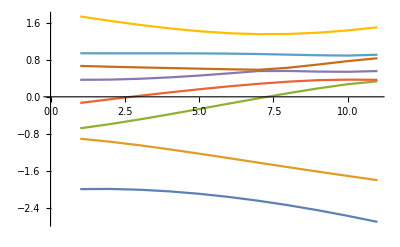

```mathematica
J =RandomReal[{-1,1},3]
h= RandomReal[{-1,1},3](* {0.8840346294055328,-0.6617186618201063,-0.5237526656637503};RandomReal[{-1,1},3]*)
ListLinePlot[Transpose[Table[s=0.05k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];Sort[Eigenvalues[H]],{k,10,20}]]]
```

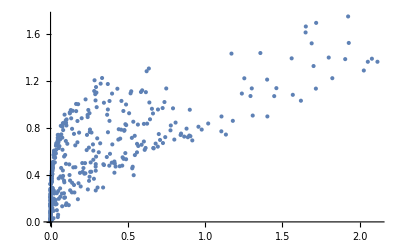

```mathematica
attmpt =Table[J =RandomReal[{-1,1},3];
h= RandomReal[{-1,1},3];
b=Table[s=0.05k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];a =Sort[Eigenvalues[H]];
a[[2]]-a[[1]]
,{k,10,20}];
{b[[-1]] -Min[b] , Min[b],J,h},{m,1,400}];
ListPlot[attmpt[[;;,1;;2]]]
```

```mathematica
al ={};
Do[ If[ attmpt[[i,1]]<0.1&&attmpt[[i,1]]>0.025 &&attmpt[[i,2]]<0.1, AppendTo[al,attmpt[[i]]],0;],{i,1,400}];
al
```

{{0.048894,0.0610755,{0.0680501,0.80657,0.841898},{-0.0267298,0.523855,0.442141}},{0.0471714,0.0408941,{-0.0714187,0.92862,-0.646706},{0.323935,0.815075,0.447107}},{0.0408977,0.0993165,{0.450486,0.614635,0.192791},{-0.241604,-0.593341,-0.547878}}}

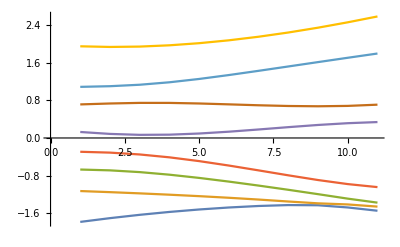

```mathematica
J ={-0.07141870283231233,0.9286196327352094,-0.6467055947937901};
h={0.32393491206292113,0.8150746691724549,0.44710702061640184};(* {0.8840346294055328,-0.6617186618201063,-0.5237526656637503};RandomReal[{-1,1},3]*)
ListLinePlot[Transpose[Table[s=0.05k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];Sort[Eigenvalues[H]],{k,10,20}]]]
```

```mathematica
a=Table[s=0.01k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];a =Sort[Eigenvalues[H]];
a[[2]]-a[[1]],{k,30,100}];
{Min[a],a[[-1]]}
```

{0.0408941,0.0880655}

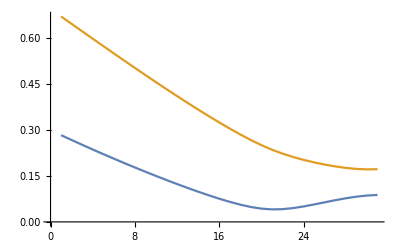

```mathematica
ListLinePlot[Transpose[Table[s=0.01k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];a =Sort[Eigenvalues[H]];
{a[[2]]-a[[1]],a[[3]]-a[[1]]},{k,70,100}]]]
```

Maybe we should use a bigger minimal gap to observe the effect of the size at these small sizes...

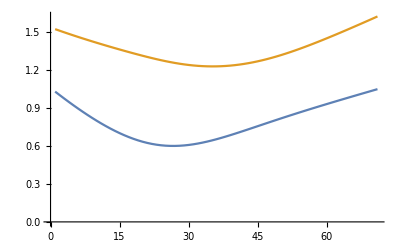

```mathematica
J ={0.9659905363673897,-0.9470136082187728,0.18650797023827392};
h= {0.33970937304614246,0.557690079109451,0.3071856129432704};
ListLinePlot[Transpose[Table[s=0.01k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];a =Sort[Eigenvalues[H]];
{a[[2]]-a[[1]],a[[3]]-a[[1]]},{k,30,100}]]]
```

```mathematica
a=Table[s=0.01k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];a =Sort[Eigenvalues[H]];
a[[2]]-a[[1]],{k,30,100}];
{Min[a],a[[-1]]}
```

{0.601168,1.05033}

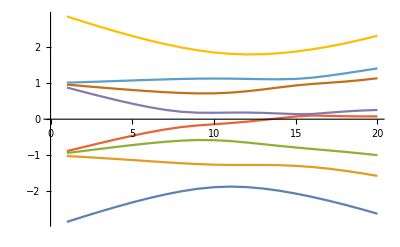

```mathematica
J ={0.9659905363673897,-0.9470136082187728,0.18650797023827392};
h= {0.33970937304614246,0.557690079109451,0.3071856129432704};(* {0.8840346294055328,-0.6617186618201063,-0.5237526656637503};RandomReal[{-1,1},3]*)
ListLinePlot[Transpose[Table[s=0.05k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];Sort[Eigenvalues[H]],{k,1,20}]]]
```

```mathematica
s=1;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
{e,v}=Eigensystem[H,5];
Table[v[[1]].At[SigZ,i].v[[1]],{i,1,c}]
```

{1.,-1.,-1.}

```mathematica
e
```

{-2.62468,2.31671,-1.57435,1.41007,1.13628}

```mathematica
b
```

{1.06728,0.997126,0.931493,0.872272,0.821645,0.781913,0.755226,0.743247,0.746824,0.765805,0.799122}

```mathematica
a
```

{-3.97079,-0.708925,-0.284776,0.0575348,0.810229,0.883311,0.936166,2.27725}

```mathematica
H
```

{{0.,0.1,0.1,0.,0.1,0.,0.,0.},{0.1,0.,0.,0.1,0.,0.1,0.,0.},{0.1,0.,0.,0.1,0.,0.,0.1,0.},{0.,0.1,0.1,0.,0.,0.,0.,0.1},{0.1,0.,0.,0.,0.,0.1,0.1,0.},{0.,0.1,0.,0.,0.1,0.,0.,0.1},{0.,0.,0.1,0.,0.1,0.,0.,0.1},{0.,0.,0.,0.1,0.,0.1,0.1,0.}}

```mathematica
s=0.1
```

0.1

```mathematica
i=1;
J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1]
```

{{0.3,0.,0.,0.,0.,0.,0.,0.},{0.,0.3,0.,0.,0.,0.,0.,0.},{0.,0.,-0.3,0.,0.,0.,0.,0.},{0.,0.,0.,-0.3,0.,0.,0.,0.},{0.,0.,0.,0.,-0.3,0.,0.,0.},{0.,0.,0.,0.,0.,-0.3,0.,0.},{0.,0.,0.,0.,0.,0.,0.3,0.},{0.,0.,0.,0.,0.,0.,0.,0.3}}

```mathematica
H= s Sum[J[[i]]At[SigZ,i].At[SigZ,Mod[i-1,c]+1],{i,1,c}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
```

9

```mathematica
dd=c/3;
```

```mathematica
J={0.3,0.7,-1};
```

```mathematica
s=0.1;
M=2;
tab =Table[s=0.02k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,1,50}];
```

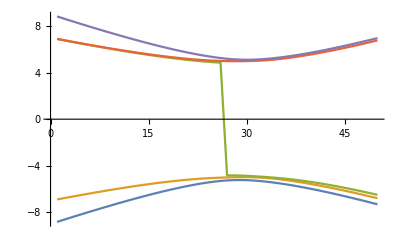

```mathematica
ListLinePlot[Transpose[tab], PlotRange->All]
```

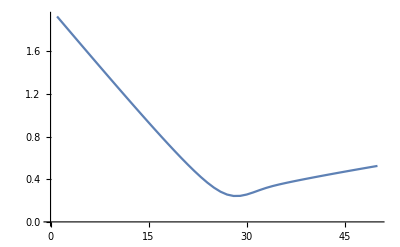

```mathematica
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
```

```mathematica
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

{0.243279,0.525166}

```mathematica
2a[[-1]]
```

1.05033

```mathematica
dd
```

3

```mathematica
c=9
```

9

```mathematica
Table[{Quotient[i-1,dd]+1, Mod[i,dd],Quotient[i,dd],Mod[i-1,c]+1},{i,1,c}]
```

{{1,1,0,1},{1,2,0,2},{1,0,1,3},{2,1,1,4},{2,2,1,5},{2,0,2,6},{3,1,2,7},{3,2,2,8},{3,0,3,9}}

```mathematica
s=1;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
{e,v}=Eigensystem[H,5];
```

```mathematica
e
```

{-7.10184,-6.89705,-6.89705,-6.89705,-6.87537}

```mathematica
Table[v[[1]].At[SigZ,i].v[[1]],{i,1,c}]
```

{1.,1.,1.,-1.,-1.,-1.,-1.,-1.,-1.}

```mathematica
Quotient[3,3]
```

1

```mathematica
Quotient[4,3]
```

1

```mathematica
Mod[0,9]
```

0

6

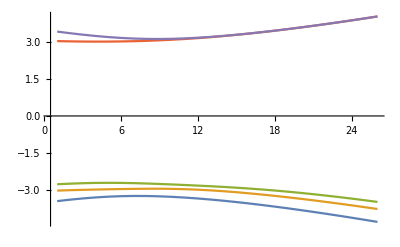

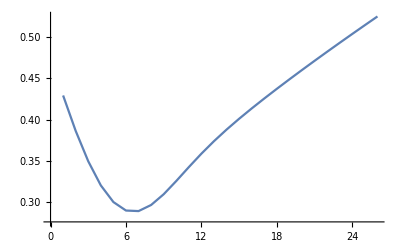

{0.288782,0.525166}

```mathematica
c=6
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=2;
tab =Table[s=0.02k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,25,50}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
{0.6011677121755605,1.050332638013158}
```

12

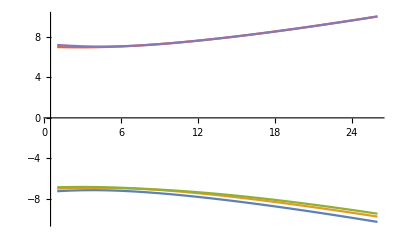

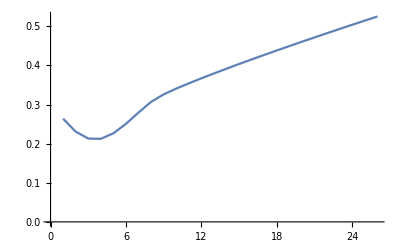

{0.212359,0.525166}

```mathematica
c=12
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=2;
tab =Table[s=0.02k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,25,50}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
lst ={0.6011677121755605, 0.28878193645002037,0.24327903964672348,0.21235899246750112};
```

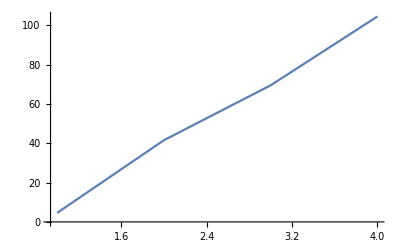

```mathematica
ListLinePlot[1/lst^3,PlotRange->All]
```

9

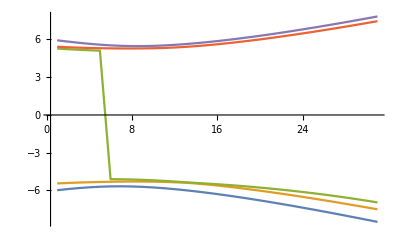

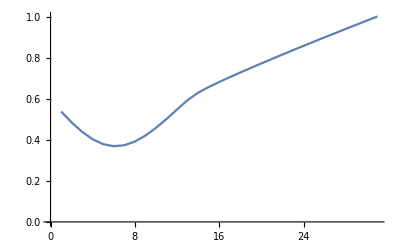

{0.368452,1.00032}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=1.05;
tab =Table[s=0.02k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,20,50}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

single qubit

9

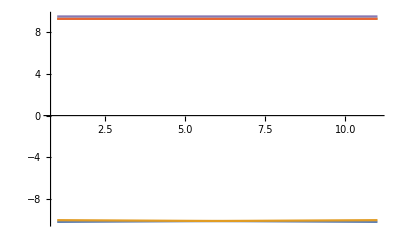

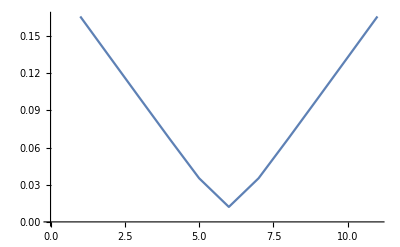

{0.0120985,0.165942}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];

tab =Table[s=0.001k;
H= 0.7 Sum[At[SigX,i],{i,1,c}] + Sum[  (1-2s)At[SigZ,i]-At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,495,505}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
J
```

{0.965991,-0.947014,0.186508}

5

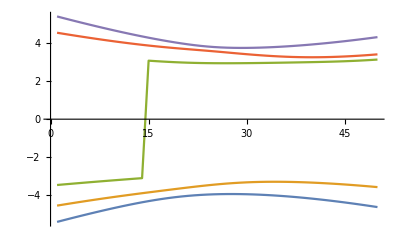

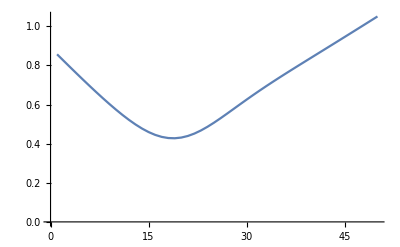

{0.42761,1.05033}

```mathematica
c=5
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];

tab =Table[s=0.02k;
H=(1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,3]+1],{i,1,3}] + Sum[  At[SigZ,i].At[SigZ,i+1],{i,3,c-1}];
Sort[Eigenvalues[H,5]],{k,1,50}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
J ={-0.07141870283231233,0.9286196327352094,-0.6467055947937901};
h={0.32393491206292113,0.8150746691724549,0.44710702061640184};
```

5

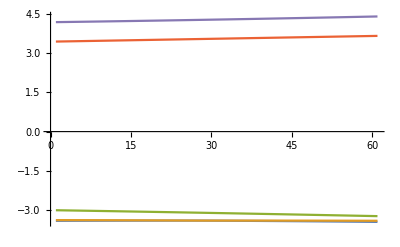

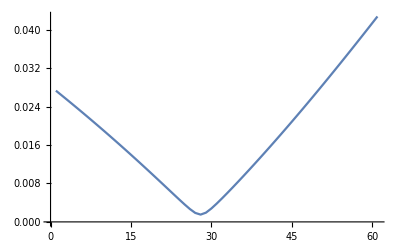

{0.00151866,0.0427428}

```mathematica
c=5
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];

tab =Table[s=0.002k;
H=(1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,3]+1],{i,1,3}] + Sum[  At[SigZ,i].At[SigZ,i+1],{i,3,c-1}];
Sort[Eigenvalues[H,5]],{k,400,460}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

9

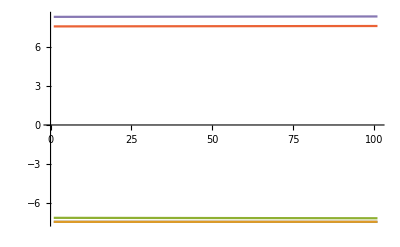

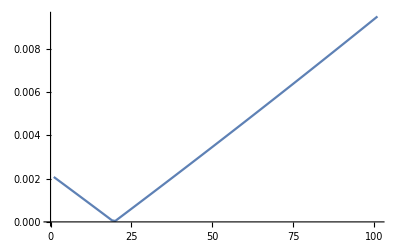

{0.0000430611,0.00950805}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];

tab =Table[s=0.0002k;
H=(1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,3]+1],{i,1,3}] + Sum[  At[SigZ,i].At[SigZ,i+1],{i,3,c-1}];
Sort[Eigenvalues[H,5]],{k,4250,4350}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

6

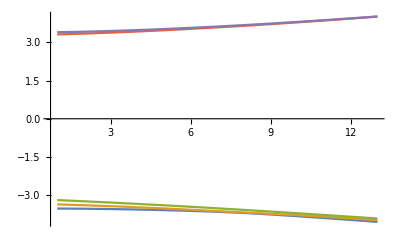

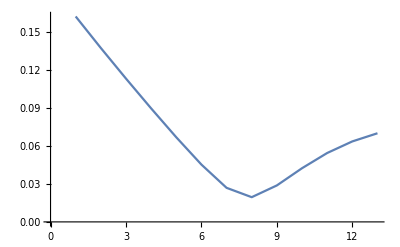

{0.0194806,0.0698763}

```mathematica
c=6
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=1.05;
tab =Table[s=0.02k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,33,45}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

12

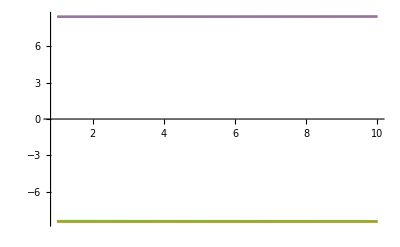

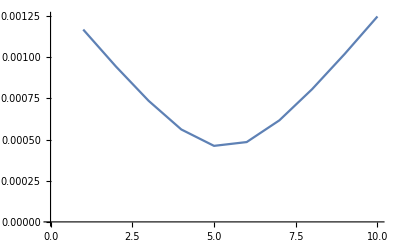

{0.000462101,0.00124855}

```mathematica
c=12
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=1.05;
tab =Table[s=0.0002k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,3940,3949}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

9

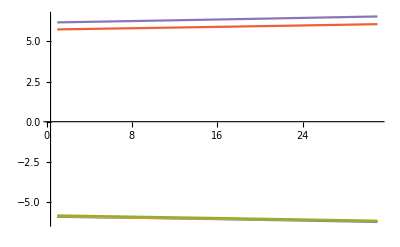

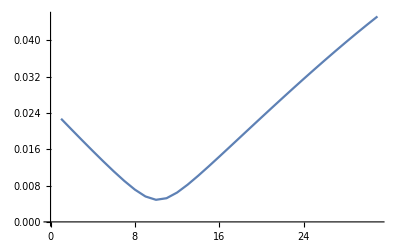

{0.00486462,0.0452412}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=1.05;
tab =Table[s=0.002k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,380,410}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
{0.019480587467762156,0.06987634899486572}
```

```mathematica
{0.040894100304413206,0.08806547298626377}
```

```mathematica
lst = {0.040894100304413206,0.019480587467762156,0.004864617308141916,0.0004621008645422364}
```

{0.0408941,0.0194806,0.00486462,0.000462101}

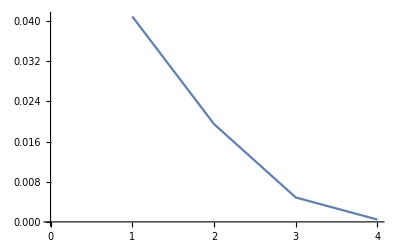

```mathematica
ListLinePlot[lst]
```

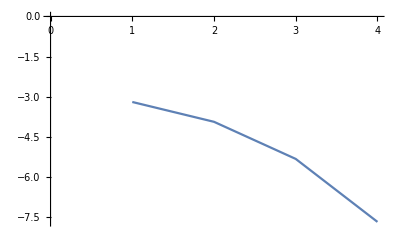

```mathematica
ListLinePlot[Log[lst]]
```

that is too fast

```mathematica
c=2
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
```

2

```mathematica
H= Sum[At[SigX,i],{i,1,c}] +At[SigZ,1]-Sum[ At[SigZ,i].At[SigZ,i+1],{i,1,c-1}];{e,v} =Eigensystem[H];
sup =v[[1]]/Sqrt[v[[1]].v[[1]]];
H= Sum[At[SigX,i],{i,1,c}] -At[SigZ,1]-Sum[ At[SigZ,i].At[SigZ,i+1],{i,1,c-1}];{e,v} =Eigensystem[H];
sdo =v[[1]]/Sqrt[v[[1]].v[[1]]];
f =N[sup.sdo]
chi =N[sup.At[SigZ,c].sup]
```

0.57735

-0.57735

9

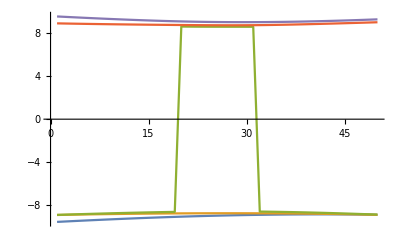

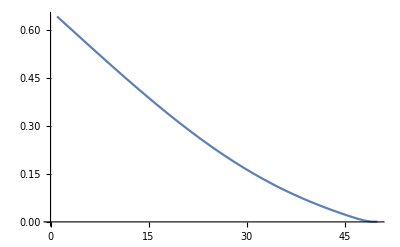

{0.000339765,0.000339765}

{9.27251,9.00318,-8.88917,-8.88883,-8.85625}

{-1.,-1.,-1.}

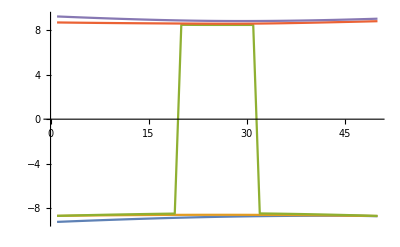

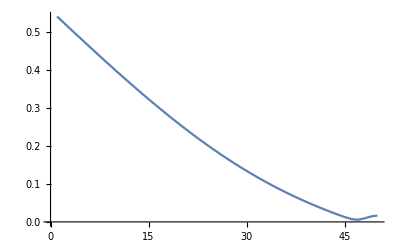

{0.00562339,0.0167985}

{1.,-1.,1.}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
alp =0.37;
tab =Table[s=0.02k;
H= Sum[If[Mod[i,dd]==1 ,0At[SigX,i],At[SigX,i]],{i,1,c}] +alp Sum[ (1-s)(1/f)At[SigX,dd(i-1)+1] +s h[[i]]At[SigZ,dd(i-1)+1],{i,1,3}] + Sum[  If[Mod[i,dd]==0,alp s J[[Quotient[i,dd]]]/(-chi),-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,1,50}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
{e,v}=Eigensystem[H,5];
e
Table[v[[3]].At[SigZ,dd(i-1)+1].v[[3]],{i,1,3}]
```

```mathematica
{e,v}=Eigensystem[H,5];
```

```mathematica
e
```

{9.05439,8.8299,-8.74329,-8.7265,-8.71687}

```mathematica
v[[3]].At[SigZ,1].v[[3]]
```

1.

its the wrong state now..

3

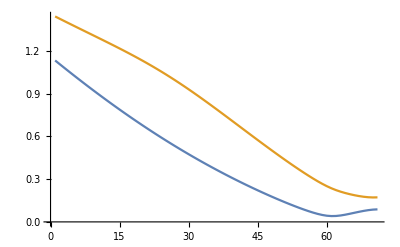

```mathematica
c=3
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
ListLinePlot[Transpose[Table[s=0.01k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] + s Sum[ h[[i]]At[SigZ,i]+ J[[i]]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];a =Sort[Eigenvalues[H]];
{a[[2]]-a[[1]],a[[3]]-a[[1]]},{k,30,100}]]]
```

```mathematica
{e,v}=Eigensystem[H,5];
```

```mathematica
e
```

{2.58499,1.79661,-1.54794,-1.45987,-1.37562}

```mathematica
Table[v[[3]].At[SigZ,i].v[[3]],{i,1,3}]
```

{1.,-1.,1.}

so it is the right state

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
```

9

so at alpha =0.37 the other state starts winning, and decreasing alpha from there is actually beneficial. There is an optimum somewhere

9

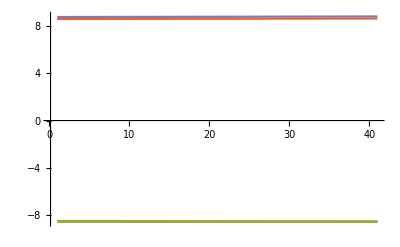

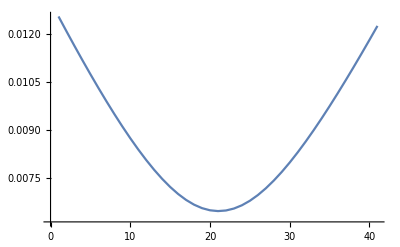

{0.00647636,0.0122638}

{8.82958,8.65608,-8.59607,-8.5838,-8.56384}

{0.978333,-0.998408,0.99312}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
alp =0.235;
tab =Table[s=0.002k;
H= Sum[If[Mod[i,dd]==1 ,0At[SigX,i],At[SigX,i]],{i,1,c}] +alp Sum[ (1-s)(1/f)At[SigX,dd(i-1)+1] +s h[[i]]At[SigZ,dd(i-1)+1],{i,1,3}] + Sum[  If[Mod[i,dd]==0,alp s J[[Quotient[i,dd]]]/(-chi),-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,440,480}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
{e,v}=Eigensystem[H,5];
e
Table[v[[3]].At[SigZ,dd(i-1)+1].v[[3]],{i,1,3}]
```

so this is the optimum, alpha =0.235, gap =0.00647636.  For the ME, optimal M=1.91, gap=0.00706. Both appear exponential

9

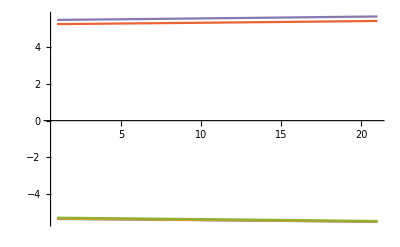

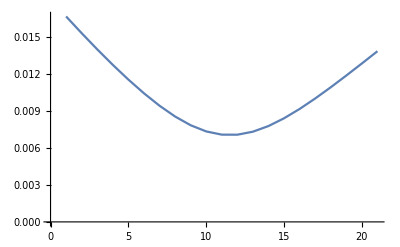

{0.00705817,0.0138161}

```mathematica
c=9
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=1.91;
tab =Table[s=0.002k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,370,390}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
{e,v}=Eigensystem[H,5];
e
Table[v[[2]].At[SigZ,dd(i-1)+1].v[[2]],{i,1,3}]
```

{5.76819,-5.58919,-5.57371,-5.53622,5.49125}

{0.933178,-0.963704,0.956809}

```mathematica
c=3
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
```

3

```mathematica
H= Sum[At[SigX,i],{i,1,c}] +At[SigZ,1]-Sum[ At[SigZ,i].At[SigZ,i+1],{i,1,c-1}];{e,v} =Eigensystem[H];
sup =v[[1]]/Sqrt[v[[1]].v[[1]]];
H= Sum[At[SigX,i],{i,1,c}] -At[SigZ,1]-Sum[ At[SigZ,i].At[SigZ,i+1],{i,1,c-1}];{e,v} =Eigensystem[H];
sdo =v[[1]]/Sqrt[v[[1]].v[[1]]];
f =N[sup.sdo]
chi =N[sup.At[SigZ,c].sup]
```

0.5

-0.5

12

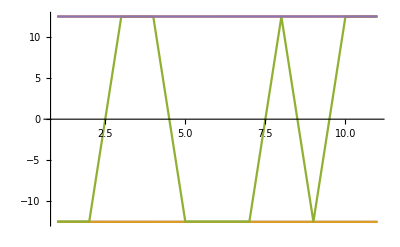

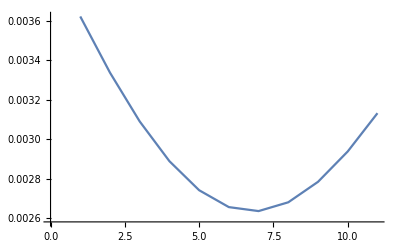

{0.00263698,0.00313266}

{12.5151,-12.5151,-12.512,12.512,-12.4884}

{-0.830871,0.970491,-0.851669}

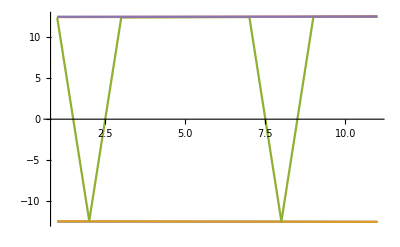

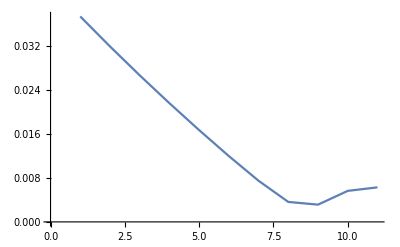

{0.00313266,0.00627037}

{-12.5342,12.5342,-12.528,12.528,-12.5135}

{-1.,-1.,-1.}

```mathematica
c=12
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
alp =0.235;
tab =Table[s=0.002k;
H= Sum[If[Mod[i,dd]==1 ,0At[SigX,i],At[SigX,i]],{i,1,c}] +alp Sum[ (1-s)(1/f)At[SigX,dd(i-1)+1] +s h[[i]]At[SigZ,dd(i-1)+1],{i,1,3}] + Sum[  If[Mod[i,dd]==0,alp s J[[Quotient[i,dd]]]/(-chi),-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,470,480}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
{e,v}=Eigensystem[H,5];
e
Table[v[[1]].At[SigZ,dd(i-1)+1].v[[1]],{i,1,3}]
```

```mathematica
Table[v[[1]].At[SigZ,dd(i-1)+1].v[[1]],{i,1,3}]
```

{1.,-1.,1.}

12

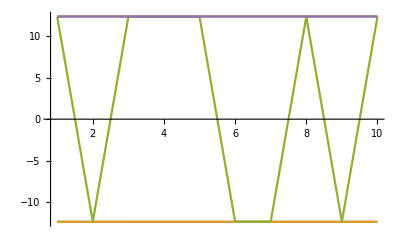

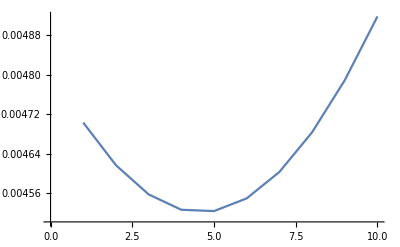

{0.00452366,0.00491835}

{12.354,-12.354,-12.3491,12.3491,-12.3263}

{0.769487,-0.933825,0.826791}

```mathematica
c=12
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
alp =0.16;
tab =Table[s=0.002k;
H= Sum[If[Mod[i,dd]==1 ,0At[SigX,i],At[SigX,i]],{i,1,c}] +alp Sum[ (1-s)(1/f)At[SigX,dd(i-1)+1] +s h[[i]]At[SigZ,dd(i-1)+1],{i,1,3}] + Sum[  If[Mod[i,dd]==0,alp s J[[Quotient[i,dd]]]/(-chi),-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,456,465}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
{e,v}=Eigensystem[H,5];
e
Table[v[[2]].At[SigZ,dd(i-1)+1].v[[2]],{i,1,3}]
```

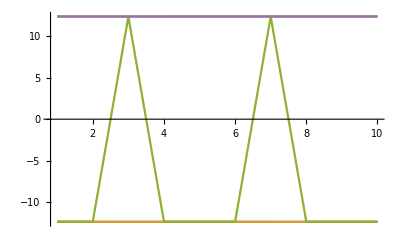

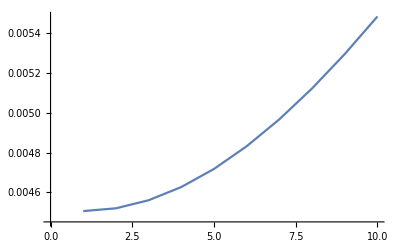

{0.00450545,0.00548422}

{12.3457,-12.3457,-12.3402,12.3402,-12.3198}

{0.869102,-0.969447,0.913871}

```mathematica
0.155
```

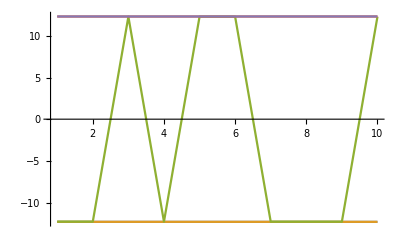

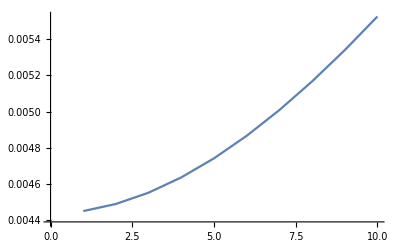

{0.00445158,0.00552477}

{12.3267,-12.3267,-12.3212,12.3212,12.302}

{0.885263,-0.974746,0.928905}

```mathematica
0.145
```

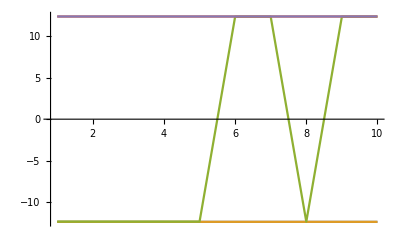

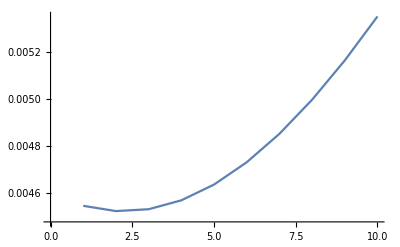

{0.00452465,0.00534852}

{12.3649,-12.3649,-12.3596,12.3596,-12.3379}

{0.846118,-0.961857,0.892265}

```mathematica
0.165
```

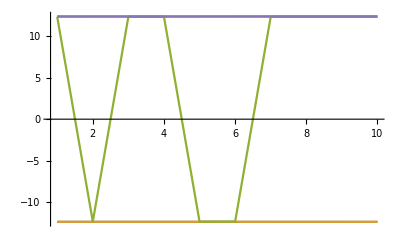

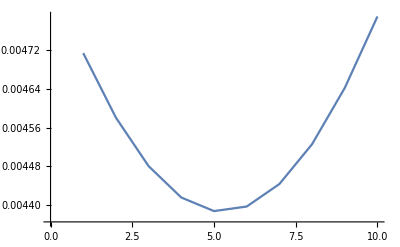

{0.00438733,0.00478952}

{12.4041,-12.4041,-12.3993,12.3993,-12.3749}

{0.759015,-0.932845,0.808989}

```mathematica
0.185
```

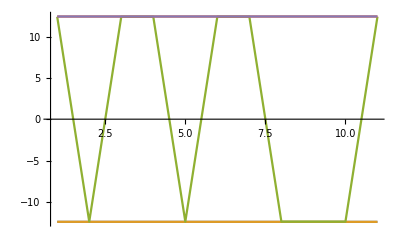

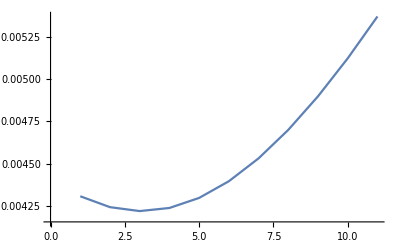

{0.00421778,0.00537311}

{-12.427,12.427,-12.4216,12.4216,-12.3994}

{-0.879446,0.974125,-0.912829}

```mathematica
0.195
```

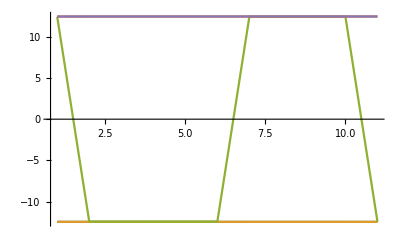

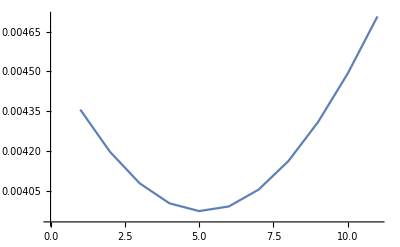

{0.00397252,0.00470707}

{12.4473,-12.4473,-12.4426,12.4426,-12.4189}

{0.830381,-0.960393,0.865793}

```mathematica
0.205
```

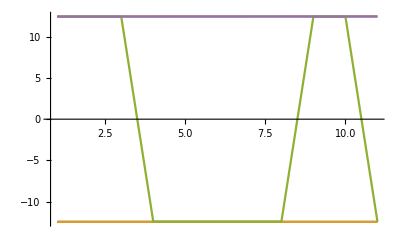

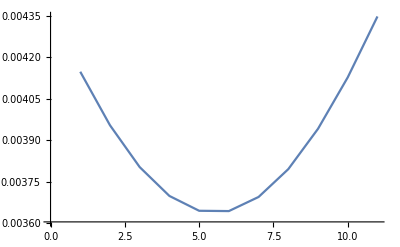

{0.00364453,0.0043467}

{12.4692,-12.4692,-12.4649,12.4649,-12.4411}

{0.833504,-0.96351,0.864415}

```mathematica
0.215
```

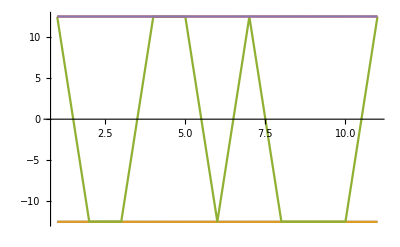

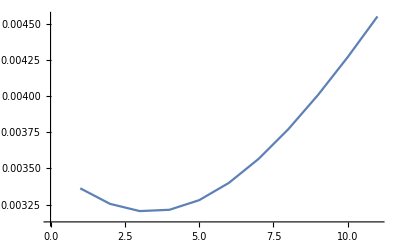

{0.00320476,0.00454873}

{12.4939,-12.4939,-12.4893,12.4893,-12.4678}

{0.922095,-0.987963,0.940482}

```mathematica
0.225
```

12

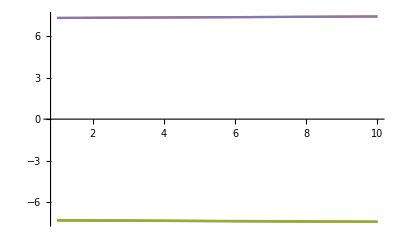

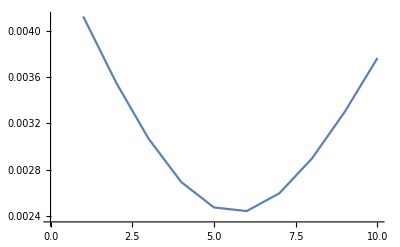

{0.002442,0.0037657}

{-7.4174,-7.41364,7.41022,7.40838,-7.39692}

{0.836985,-0.932641,0.868708}

```mathematica
c=12
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=4.2;
tab =Table[s=0.002k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,369,378}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
{e,v}=Eigensystem[H,5];
e
Table[v[[1]].At[SigZ,dd(i-1)+1].v[[1]],{i,1,3}]
```

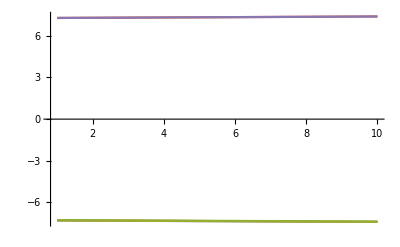

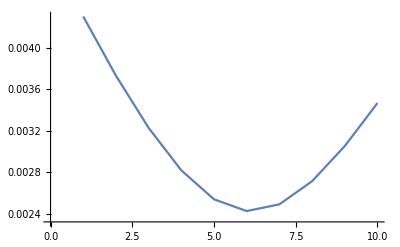

{0.00242659,0.00346777}

{-7.40572,-7.40225,7.39875,7.39705,-7.38576}

{0.807412,-0.926312,0.842448}

```mathematica
4.4
```

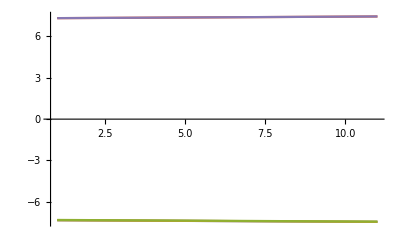

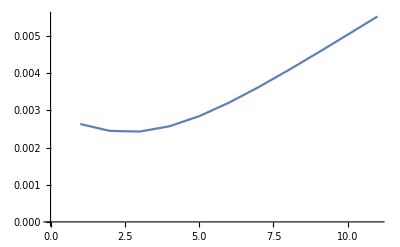

{0.00242866,0.00552426}

{-7.45667,-7.45115,7.45005,7.44862,-7.43793}

{0.923687,-0.951896,0.944249}

```mathematica
4.6
```

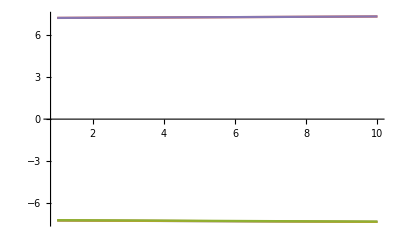

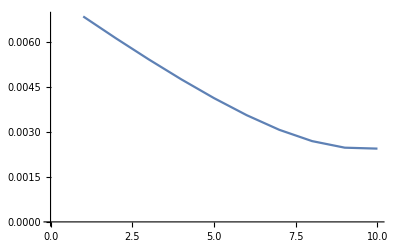

{0.002442,0.002442}

{-7.36971,-7.36726,7.36195,7.35998,-7.34806}

{0.311147,-0.814768,0.372258}

```mathematica
4.2
```

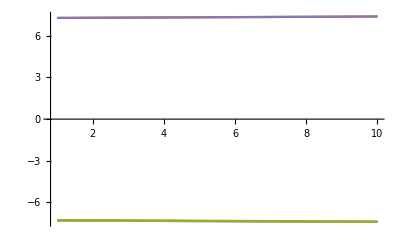

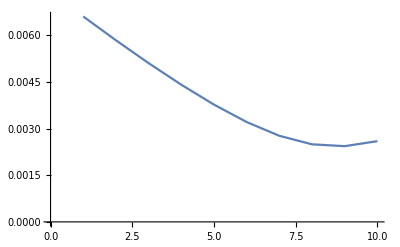

{0.00243473,0.00259586}

{-7.39618,-7.39358,7.38813,7.38578,-7.37355}

{0.515218,-0.866301,0.565883}

```mathematica
3.8
```

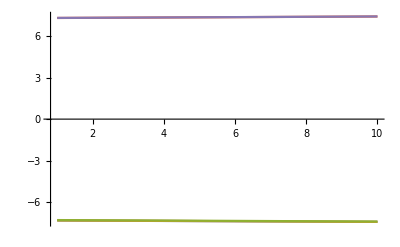

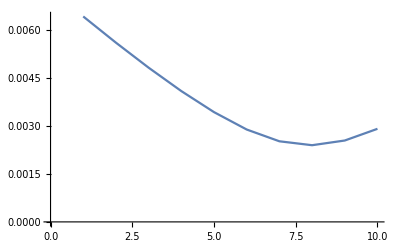

{0.0023985,0.0029113}

{-7.42912,-7.42621,7.4206,7.41775,-7.40516}

{0.673614,-0.90233,0.714242}

```mathematica
3.4
```

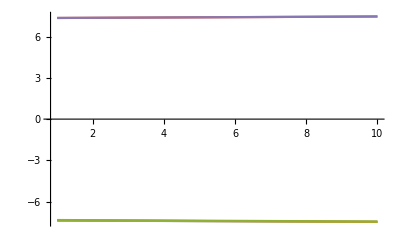

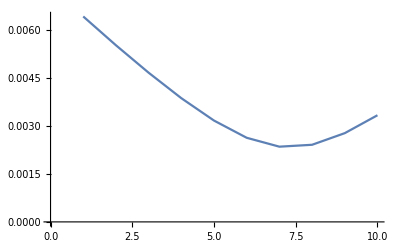

{0.00234683,0.00332749}

{-7.47113,-7.46781,7.46195,7.45841,-7.44537}

{0.776293,-0.923423,0.808696}

```mathematica
3
```

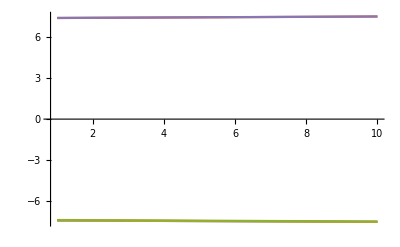

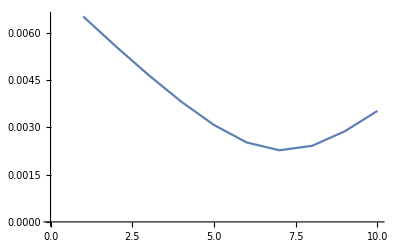

{0.002276,0.00352704}

{-7.49676,-7.49324,7.48716,7.48317,-7.46988}

{0.809483,-0.929854,0.838657}

```mathematica
2.8
```

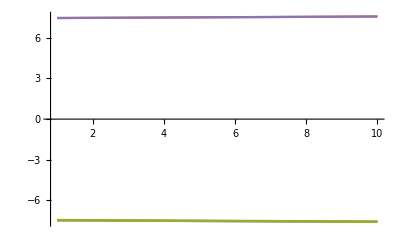

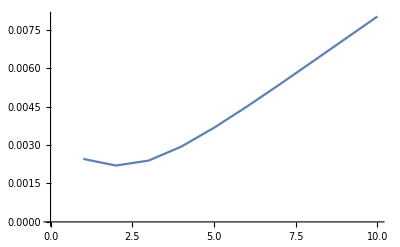

{0.0021994,0.00801742}

{-7.59033,-7.58232,7.58012,7.57597,-7.5625}

{0.94592,-0.952561,0.959578}

```mathematica
2.6
```

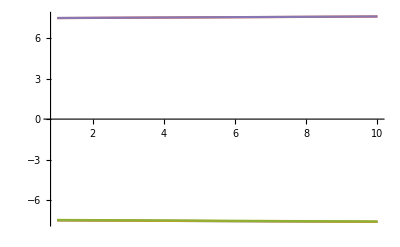

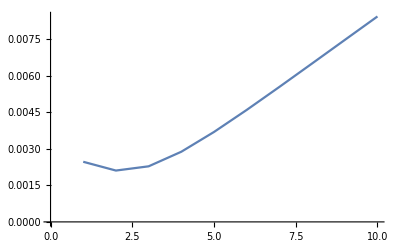

{0.00211119,0.00844722}

{-7.6258,-7.61735,7.61494,7.6102,-7.59632}

{0.949596,-0.953215,0.962282}

```mathematica
2.4
```

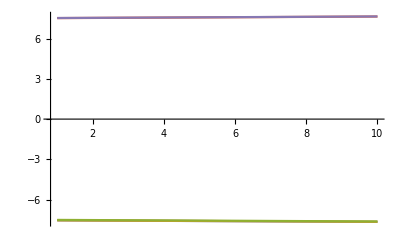

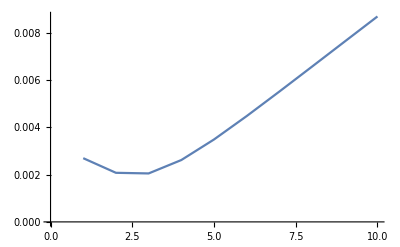

{0.00205278,0.00870231}

{-7.66784,-7.65913,7.65623,7.65075,-7.63641}

{0.952654,-0.953862,0.96452}

```mathematica
2.2
```

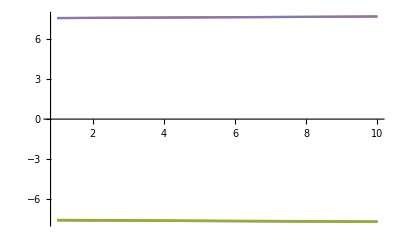

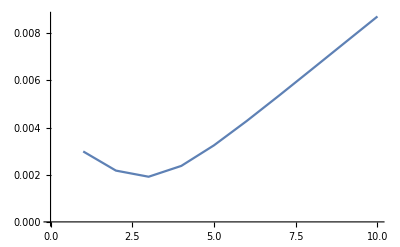

{0.00191489,0.00871047}

{-7.69191,-7.6832,7.67989,7.67397,-7.65937}

{0.953918,-0.95419,0.965438}

```mathematica
2.1
```

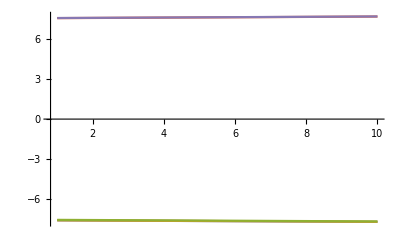

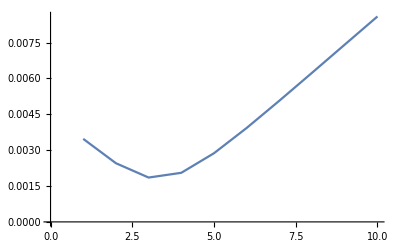

{0.00185483,0.00859218}

{-7.71844,-7.70984,7.70597,7.69955,-7.68468}

{0.954941,-0.954525,0.966166}

```mathematica
2
```

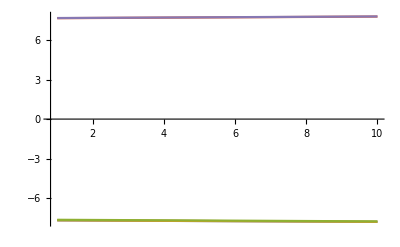

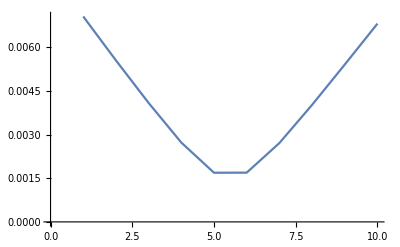

{0.00168796,0.00680689}

{-7.8171,-7.8103,7.80303,7.79467,-7.77887}

{0.953938,-0.955501,0.964905}

```mathematica
1.7
```

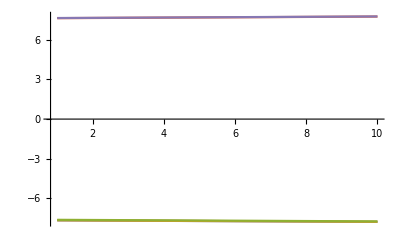

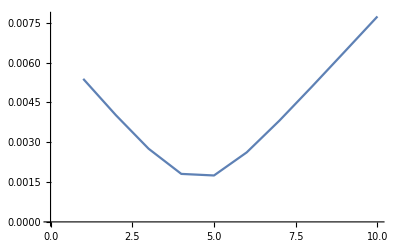

{0.00174824,0.00773633}

{-7.78049,-7.77276,7.767,7.75938,-7.74391}

{0.955558,-0.955201,0.966435}

```mathematica
1.8
```

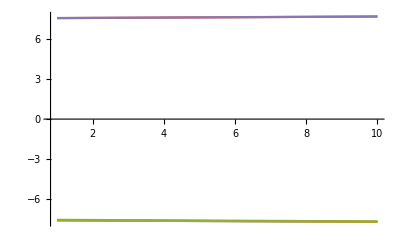

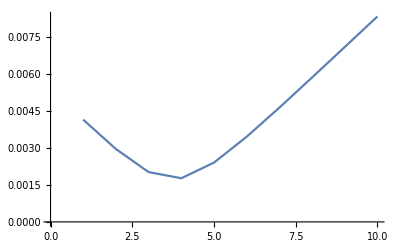

{0.00177021,0.00833342}

{-7.74473,-7.73639,7.73182,7.7249,-7.70977}

{0.95555,-0.954831,0.966567}

```mathematica
1.91
```

```mathematica
lstME ={0.040894100304413206,0.019501841073968684,0.007058174727093913,0.0024420015699178066};
```

```mathematica
lstPT ={0.040894100304413206,0.011443049479134437,0.0064763571202188785,0.004524645671267535};
```

6

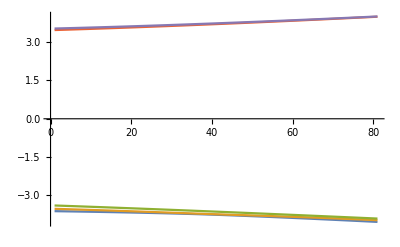

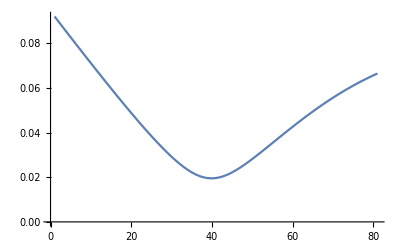

{0.0195018,0.0664509}

```mathematica
c=6
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
M=1;
tab =Table[s=0.002k;
H= (1-s) Sum[At[SigX,i],{i,1,c}] +s Sum[ (1/(M dd))h[[Quotient[i-1,dd]+1]]At[SigZ,i]+ If[Mod[i,dd]==0,J[[Quotient[i,dd]]]/M,-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,360,440}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
```

```mathematica
H= SigX +SigZ;
{e,v} =Eigensystem[H];
sup =v[[1]]/Sqrt[v[[1]].v[[1]]];
H= SigX -SigZ;
{e,v} =Eigensystem[H];
sdo =v[[1]]/Sqrt[v[[1]].v[[1]]];
f =N[sup.sdo]
chi =N[sup.SigZ.sup]
```

0.707107

-0.707107

6

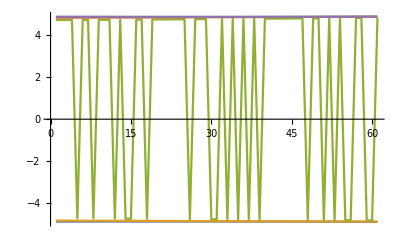

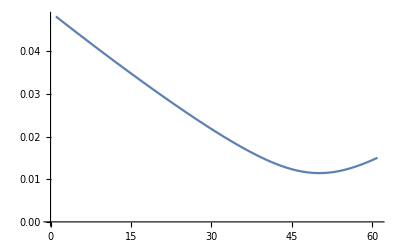

{0.011443,0.0150378}

{4.88216,-4.88216,4.86712,-4.86712,-4.81671}

{0.903847,-0.980258,0.941829}

```mathematica
c=6
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
dd=c/3;
alp =0.4;
tab =Table[s=0.002k;
H= Sum[If[Mod[i,dd]==1 ,0At[SigX,i],At[SigX,i]],{i,1,c}] +alp Sum[ (1-s)(1/f)At[SigX,dd(i-1)+1] +s h[[i]]At[SigZ,dd(i-1)+1],{i,1,3}] + Sum[  If[Mod[i,dd]==0,alp s J[[Quotient[i,dd]]]/(-chi),-1]At[SigZ,i].At[SigZ,Mod[i,c]+1],{i,1,c}];
Sort[Eigenvalues[H,5]],{k,410,470}];
ListLinePlot[Transpose[tab], PlotRange->All]
ListLinePlot[tab[[;;,2]] -tab[[;;,1]]]
a=tab[[;;,2]] -tab[[;;,1]];
{Min[a],a[[-1]]}
{e,v}=Eigensystem[H,5];
e
Table[v[[2]].At[SigZ,dd(i-1)+1].v[[2]],{i,1,3}]
```

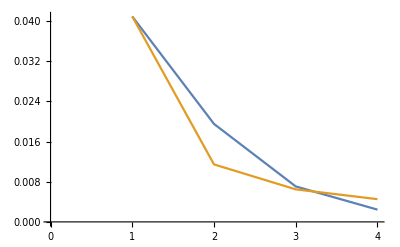

```mathematica
ListLinePlot[{lstME,lstPT}]
```

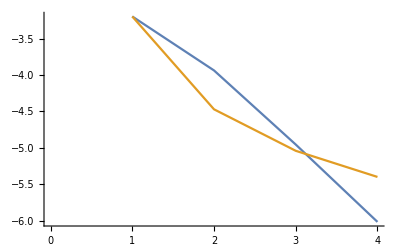

```mathematica
ListLinePlot[{Log[lstME],Log[lstPT]}]
```

```mathematica
lstAlp ={1,0.4,0.235,0.16};
lstOvM = {1,1,1/1.91,1/4.2};
```

```mathematica
Superscript
```

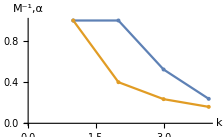

```mathematica
Show[ListLinePlot[{lstOvM,lstAlp},AxesLabel->{"k","M^-1,α"},AxesStyle->Black,PlotLegends->{"M^-1","α"}],
ListPlot[{lstOvM,lstAlp},AxesLabel->{"k","M^-1,α"},AxesStyle->Black]]
```

```mathematica
(*,AxesLabel->{"n","1/Δs_r"},AxesStyle->Thick,BaseStyle->{FontWeight->Bold,FontSize->12},PlotLabel-> "Extended"*)
```

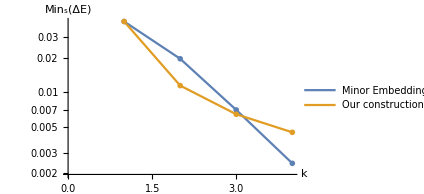

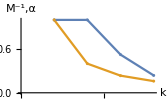

```mathematica
ListLogPlot[{lstME,lstPT},AxesLabel->{"k","Min_s(ΔE)"},AxesStyle->Black,PlotLegends->{"Minor Embedding","Our construction"},Joined->True,Mesh->All]
```

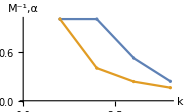

```mathematica
ListPlot
```